## Introduction

The “Barium” package basically contains everything needed to simulate MS gates.

This package does quantum using matrix mechanics. Operators are represented by matrices and states are represented by vectors. We generate our state space by taking the outer product of all the independent bases, so only one vector is needed to hold all the states, and all the operators have the same dimensions.

An unreasonable amount of time has been wasted trying to make everything as fast as can be: nearly everything is done (close to) instantaneously, with the exception of the Schrodinger Solver and (only for very large state spaces, >10,000) the GetPoints function, and even those have been sped up significantly. This is done by basically not using Mathematica as it’s meant to be used - all evaluation is left as late as possible to allow us to do so numerically, as opposed to using symbols. None of the functions or operators are designed to handle symbols; use symbols at your own risk.

Additionally, none of the packaged functions use parallelization. This is to allow the user to choose when/which functions to parallelize, since Mathematica only allows us to parallelize once.

Without any off-resonant terms, a regular, full, MS gate should take less than 5 seconds to solve. Including off-resonant terms within a few orders of magnitude of the dominant behavior adds roughly a factor of 10 to the computation time. For example, if we included the counter-rotating terms at twice the qubit transition (4 - 5 orders of magnitude about the detuning) as well as the carrier (3 - 4 orders of magnitude above the terms rotating at twice the qubit transition), NDSolve would take ~100 x as long. Also, note that including off- resonant terms will also eat up memory like no tomorrow, and if very, very off-resonant, can eat up all the RAM and cause a crash.

The package mainly consists of 5 parts:
1) The data generator: this basically takes trap and ion parameters and returns normal mode data as well as matches them to the operators/states.
For example, once the secular frequency has been specified through the trap parameters, ThermalState will use it to generate a Boltzmann distribution.
2) Quantum operators: the user-specified configuration is automatically reflected in these. These are held in arrays corresponding to the number of qubits and modes specified.
3) Hamiltonians: these generate Hamiltonians from the specified configuration and from user arguments.
4) the Schrodinger Solver: this basically numerically solves the interaction picture Schrodinger equation between two given points in time for the specified Hamiltonian.
5) data processing functions: these convert the wavefunctions from the Schrodinger solver into recognizable results, such as qubit state populations or average phonon numbers in each mode.

There isn’t as much stuff in this package as the EGGs package because I’m mostly going off the needs of the 213B class, but I’ll be porting the features over from the EGGs packages - expect more updates soon.

## Setup

When the package is loaded, a dialog box will open, prompting the user to enter their desired values (please make sure they are all numeric).

```mathematica
<<Barium`
```

## Sample Case 1: Applying an On-Resonant Carrier Hamiltonian

This part looks a lot longer than it is, mostly because I’ve gone into a fair amount of detail on each part. Subsequent sample cases will better demonstrate how quickly we can start running gates.
In this example, we will be applying an on-resonant carrier Hamiltonian to both ions in the trap.

## Set Variables

Quick heads up: we’re not actually “setting” variables here (as in evaluating these variables won’t have any effect), but just storing them for clarity later on.
Each Hamiltonian requires a rabi frequency, a detuning, the mode to be operated on, the direction (i.e. radial or axial), and a phase.

```mathematica
Ω1=2π*1*^6;(*set rabi frequency to 1 x 2π MHz*)
δ1=0;(*on resonance with transition*)
dir1=1;(*target radial direction; 1 is radial, 2 is axial*)
ϕ1=0;(*set phase of laser to 0*)
```

## Get Hamiltonian

The basic Hamiltonians involved in constructing an MS gate are included, as well as certain Hamiltonians which make life easier, such as the Hamiltonian for an MS gate itself.
If the desired Hamiltonian is not included, users can use the operators to create the desired Hamiltonian.

When we specify the mode argument for Hamiltonian functions, we are specifying which mode we want the Hamiltonian to be applied to. For example, if our Hamiltonian is detuned to the radial CoM mode, but we apply the Hamiltonian to the radial rocking mode, we won’t see much behavior.

```mathematica
(*we manually apply the hamiltonian to the desired ions across all modes*)
Ham1=Sum[HCarrier[Ω1,δ1,ϕ1,ion,mode,dir1],{ion,2},{mode,2}];
```

We still need to transform our Hamiltonian into the interaction picture with respect to the trap.

```mathematica
(*get time evolution operator for trap in radial direction across all modes*)
Uint1=Dot[Ut[[dir1,1]],Ut[[dir1,2]]];
```

```mathematica
(*take hamiltonian into interaction picture*)
Hint1=ToIntPic[Ham1,Uint1];
```

## Solve Schrodinger Equation

### Generating States

While users can simply create vectors with their desired populations, the use of outer products to define the basis makes it makes it tricky to tell which element of the basis corresponds to which state. To simplify this, the function PureState returns a vector with population of 1 in the desired state. Thermal states and Coherent states can also be created using ThermalState and CoherentState, respectively.
Also, while the function name PureState sort of implies support for mixed states, I only named it that because I couldn’t think of a better name for a regular, normal state; there is no support for mixed states.

```mathematica
(*we want to initialize our ions in the ground state: both ions are in gg, and have no phonon population*)
(*the first value argument specifies the qubit state, while the second specifies the phonon number in each mode*)
initstate1=PureState[{0,0},{0,0}];
```

```mathematica
(*alternatively, we could call GroundState, which returns the motional ground state in the specified qubit state*)
initstate1=GroundState[{0,0}];
```

```mathematica
(*set parameters for solving the schrodinger equation*)
tmin1=0;tmax1=1*^-6;
```

### Solving the Schrodinger Equation

SolveSchrodinger takes in a Hamiltonian matrix and solves the Time-Dependent interaction picture Schrodinger equation. SolveSchrodinger requires all input to be numeric (i.e. no symbols) with the except of “t”, which is treated as the independent variable for NDSolve. SolveSchrodinger returns a dispatch table, which is basically a bunch of replacement rules in a black box to make replacement go faster. This means that if you want to look at the constituent solutions (e.g. the result for ψ1[t]), you need to apply the dispatch table to the individual function, or to ψBasis, which holds the symbols for all the wavefunctions.

```mathematica
(*solve!*)
res1=SolveSchrodinger[Hint1,initstate1,tmin1,tmax1];
```

```mathematica
(*works!*)
resWavefunctions=ψBasis[[1]]/.res1
```

InterpolatingFunction[…][t]

```mathematica
(*doesn't work*)
res1[[1]]
```

Part::partd: Part specification … is longer than depth of object.

Dispatch[<484>]⟦1⟧

## Plot

### Getting Populations and Plotting

Since it can be bothersome and computationally cumbersome to correctly group the wavefunctions in our basis to yield information such as populations or phonon numbers, in-house functions have been written to quickly do this.
For example, GetPops returns the populations of each qubit state.

```mathematica
(*GetPops converts the wavefunctions into populations for each qubit state*)
resPops1=GetPops[res1];
```

```mathematica
(*plot!*)
Plot[resPops1,{t,tmin1,tmax1},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large]
```

-Graphics-

### Using GetPoints and ListPlot

While we can simply use Plot when we have nice behavior, doing so for fast-oscillating results will take forever. To get around this, we can instead use GetPoints to quickly get a number of points and use ListPlot.

```mathematica
(*get points*)
numPoints1=300;
resPopsPoints1=GetPoints[resPops1,tmin1,tmax1,numPoints1];
```

```mathematica
(*use listplot*)
ListPlot[Transpose[resPopsPoints1],DataRange->{tmin1,tmax1},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large]
```

-Graphics-

## Sample Case 2: Applying Sidebands

Now that we’ve started walking, we can begin a light jog.
In this example, we will be applying a red- and blue-detuned sideband pulse to both ions.

## Set Variables

Since we’re applying sidebands, we now need to change Δk for our ions. Let’s pretend we’re using counter-propagating 729nm lasers (Δk = 2x(2π)/(729 nm)) detuned to the CoM motional sideband (δω = ω_1)
To change the variables, we have to call ChangeVariables, which opens up a dialog box to change variables.

```mathematica
ChangeAll[];
```

Again, we set our desired variables:

```mathematica
Ω2=2π*1*^6;(*set rabi frequency to 1 x 2π MHz*)
δ2=wmvals[[1,1]];(*detuned to the radial CoM sideband*)
dir2=1;(*target radial direction; 1 is radial, 2 is axial*)
ϕ2=0;(*set phase of laser to 0*)
```

## Get Hamiltonians

We can create 4 types of Hamiltonians: the carrier Hamiltonian, the red sideband Hamiltonian, the blue sideband Hamiltonian, and the “bad” Hamiltonian (I believe this contains the self-transitions). Please note that these Hamiltonians only give components of a single pulse. For a complete pulse, we would need all four components.
Separating the components of a single pulse this way is advantageous since it allows us to decide what matters and what doesn’t. For example, if we were applying a very blue-detuned pulse, the red sideband component of that pulse would be far off-resonance and thus negligible. Including only the carrier and blue sideband terms is thus equivalent to applying the RWA.

For this exercise, we want to apply two sideband pulses on-resonance with the first motional sideband, which should heat the ions (useful for readout). If we assume that the ion offsets are zero, we can ignore the carrier Hamiltonian and “bad” Hamiltonians.

```mathematica
Hlower2=Sum[Hrsb[Ω2,-δ2,ϕ2,ion,mode,dir2]+Hbsb[Ω2,-δ2,ϕ2,ion,mode,dir2],{ion,2},{mode,{1,2}}];
Hupper2=Sum[Hrsb[Ω2,δ2,ϕ2,ion,mode,dir2]+Hbsb[Ω2,δ2,ϕ2,ion,mode,dir2],{ion,2},{mode,{1,2}}];
```

```mathematica
(*get time evolution operator for trap in radial direction across all modes and transform into interaction picture*)
Uint2=Dot[Ut[[dir2,1]],Ut[[dir2,2]]];
Hint2=ToIntPic[Hlower2+Hupper2,Uint2];
```

## Solve Schrodinger Equation and Plot

### Solving

```mathematica
(*we don't choose the ground state here since we need some phonons for our sideband hamiltonians to act on*)
initstate2=PureState[{0,0},{0,0}];
(*choose our calculation time*)
tmin2=0;tmax2=50*^-6;
```

```mathematica
(*solve and get pops*)
res2=SolveSchrodinger[Hint2,initstate2,tmin2,tmax2];
resPops2=GetPops[res2];
```

We are also interested in the average phonon numbers. This can be given by GetPhonons, which gives the number of phonons in the specified mode.
Specifically, we want to know the number of phonons in the radial CoM mode (mode 1) over time.

```mathematica
resPhonons2=GetPhonons[res2,1,dir2];
```

### Plotting

```mathematica
(*plot qubit states*)
Plot[resPops2,{t,tmin2,tmax2},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large]
```

-Graphics-

Our result for average phonon number shows unexpected oscillatory behavior. This is because the max phonon number is too low; once the phonons hit the top, they start coming back down again, yielding this behavior.
The simple solution is just to increase the max phonon number, though be careful that you don’t go too high: 10 phonons in 2 modes for 2 qubits only requires 400 states, but the same for 20 phonons requires 1600.

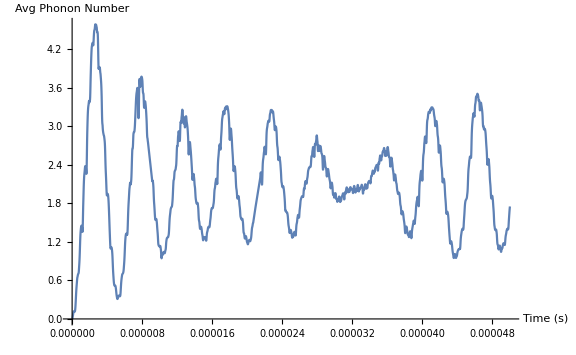

```mathematica
(*plot average phonon number*)
Plot[resPhonons2,{t,tmin2,tmax2},AxesLabel->{"Time (s)","Avg Phonon Number"},ImageSize->Large]
```

## Sample Case 3: Doing an MS Gate

Let’s upgrade to a speedy jog, just below a sprint.
In this example, we will be applying an MS gate to our ions.

## Set Variables

No need to change variables here, as long as Δk is nonzero.

```mathematica
Ω3=75*2π*1*^3;(*set rabi frequency to 75 x 2π kHz*)
Ωbad3=1.5*2π*1*^6;(*set rabi frequency to 1.5 x 2π MHz*)
δ3=wmvals[[1,1]];(*detuned to the radial CoM sideband*)
dir3=1;(*target radial direction; 1 is radial, 2 is axial*)
ϕ3=0;(*set phase of laser to 0*)
δdetune3=75*2*π*1*^3;(*our pulse is off resonance by 75 x 2π kHz*)
```

## Get Hamiltonian

To do an MS gate, we need to apply two pulses, each symmetrically detuned from a motional sideband (δDJ, which we choose to be the radial CoM sideband). For each pulse (which we call H_lower and H_upper), we want to include all four components: the carrier Hamiltonian, the red and blue sidebands, and the “bad” stuff.

```mathematica
Hlower3=Sum[Hrsb[Ω3,-(δ3+δdetune3),ϕ3,ion,mode,dir3]+Hbsb[Ω3,-(δ3+δdetune3),ϕ3,ion,mode,dir3]+HCarrier[Ω3,-(δ3+δdetune3),ϕ3,ion,mode,dir3],{ion,2},{mode,{1,2}}]+
Sum[Hbad[Ωbad3,ion],{ion,{1,2}}];
```

```mathematica
Hupper3=Sum[Hrsb[Ω3,(δ3+δdetune3),ϕ3,ion,mode,dir3]+Hbsb[Ω3,(δ3+δdetune3),ϕ3,ion,mode,dir3]+HCarrier[Ω3,(δ3+δdetune3),ϕ3,ion,mode,dir3],{ion,2},{mode,{1,2}}]+
Sum[Hbad[Ωbad3,ion],{ion,{1,2}}];
```

Alternatively, this can be done using HAll, which contains the carrier, red sideband, and blue sideband Hamiltonians:

```mathematica
Hlower3=Sum[HAll[Ω3,(δ3+δdetune3),ϕ3,ion,mode,dir3],{ion,2},{mode,{1,2}}];
```

```mathematica
Hupper3=Sum[HAll[Ω3,-(δ3+δdetune3),ϕ3,ion,mode,dir3],{ion,2},{mode,{1,2}}];
```

```mathematica
(*get time evolution operator for trap in radial direction across all modes and transform into interaction picture*)
Uint3=Dot[Ut[[dir3,1]],Ut[[dir3,2]]];
Hint3=ToIntPic[Hlower3+Hupper3,Uint3];
```

## Solve Schrodinger Equation and Plot

### Solving

```mathematica
(*we choose the ground state for a classic MS gate*)
initstate3=PureState[{0,0},{0,0}];
(*we need to calculate for much longer since the gate time is a few hundred μs*)
tmin3=0;tmax3=100*^-6;
```

Computation times are beginning to take a while...

```mathematica
(*solve and get pops*)
res3=SolveSchrodinger[Hint3,initstate3,tmin3,tmax3];
resPops3=GetPops[res3];
```

### Plotting

Since we might get very oscillatory behavior, we just use GetPoints and ListPlot for simplicity.

```mathematica
numPoints3=300;
resPopsPoints3=GetPoints[resPops3,tmin3,tmax3,300];
```

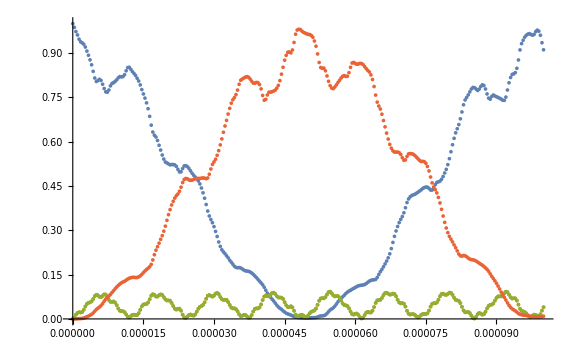

```mathematica
ListPlot[resPopsPoints3//Transpose,ImageSize->Large,DataRange->{tmin3,tmax3}]
```

Let’s also check that we’re not missing anything by plotting the whole thing:

```mathematica
(*plot!*)
Plot[resPops3,{t,tmin3,tmax3},PlotRange->{0,1},PlotLabels->{"00","01","10","11"},AxesLabel->{"Time (s)","Population"},ImageSize->Large]
```

-Graphics-

We can get a prettier MS gate by changing the detuning to the ideal value specified by the original paper.

### Fidelity

With MS gates, the result we are most interested in is the fidelity; specifically, the Bell State fidelity. To get the fidelity, we can use GetFidelity, which requires users to specify the desired qubit state (for us, that would be a Bell State).

```mathematica
bellState3=1/(√2){1,0,0,ⅈ};(*this is gg + i * ee*)
```

We want to get the fidelity over time:

```mathematica
resFid3=GetFidelity[res3,bellState3];
resFidPoints3=GetPoints[resFid3,tmin3,tmax3,numPoints3];
```

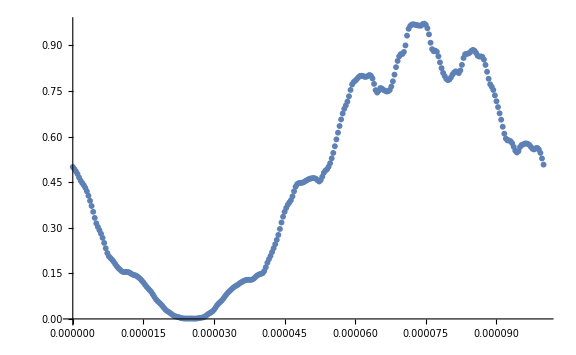

```mathematica
ListPlot[resFidPoints3//Transpose,ImageSize->Large,DataRange->{tmin3,tmax3}]
```

The maximum fidelity is:

```mathematica
Max[resFidPoints3]
```

0.971545

## Sample Case 4: Hand-Building a Hamiltonian

Finally, we can start sprinting.
In this example, I’ll try to show what goes into building the carrier Hamiltonian for a single pulse to try and demonstrate how arbitrary Hamiltonians can be built.

## Set Variables

Let us first declare the variables we’ll need for the carrier Hamiltonian:

```mathematica
Ω4=2π*1*^6;(*set rabi frequency to 75 x 2π kHz*)
δ4=0;(*on resonance*)
dir4=1;(*target radial direction; 1 is radial, 2 is axial*)
ϕ4=0;(*set phase of laser to 0*)
Δ4=80*2*π*1*^6;(*just choosing random values*)
ℏ=(6.626*^-34)/(2π);
```

## Create Hamiltonian

The carrier Hamiltonian is given by:

-ℏΩ/2∑_(p'≠p) (ⅇ^(ⅈ(Δk R_0-Δϕ-δω t))((D̂)_0)^(i)(σ_+)^(i)+h.c.)

where ((D̂)_0)^(i)is the Debye-Waller factor (including the phonon creation/annihilation operators).

We first factor out the scalar terms:

```mathematica
H4coeff=(-ℏ Ω4)/2;
```

Then the exponential term (assume R_0 = 0):

```mathematica
H4exp=Exp[ⅈ*(-ϕ4-δ4*t)];
```

Then the Debye-Waller term (we’re summing over all radial modes):

```mathematica
(*the first argument (here 0) specifies the order of the Debye-Waller factor, the second argument specifies the ion*)
H4dwion1=Sum[Dni[0,1,mode,dir4],{mode,{1,2}}];
H4dwion2=Sum[Dni[0,2,mode,dir4],{mode,{1,2}}];
```

Then the qubit terms:

```mathematica
H4ion1=σp[[1]];
H4ion2=σp[[2]];
```

Bringing it all together:

```mathematica
Hint4=H4coeff*(H4exp*(H4dwion1.H4ion1+H4dwion2.H4ion2));
```

Adding the complex conjugate terms:

```mathematica
Hint4+=Simplify[ConjugateTranspose[Hint4],t∈Reals];
```

## Solve Schrodinger Equation and Plot

### Solving

```mathematica
initstate4=GroundState[{0,0}];
```

```mathematica
(*let's try a coherent state this time, for no other reason than for fun*)
(*temp3=5*^-4;(*0.5 mK thermal state*)
initstate3=ThermalState[{0,0},temp3];*)
(*we need to calculate for much longer since the gate time is a few hundred μs*)
tmin4=0;tmax4=1*^-6;
```

```mathematica
(*solve and get pops*)
res4=SolveSchrodinger[Hint4,initstate4,tmin4,tmax4];
resPops4=GetPops[res4];
```

### Plotting

```mathematica
numPoints4=300;
resPopsPoints4=GetPoints[resPops4,tmin4,tmax4,numPoints4];
```

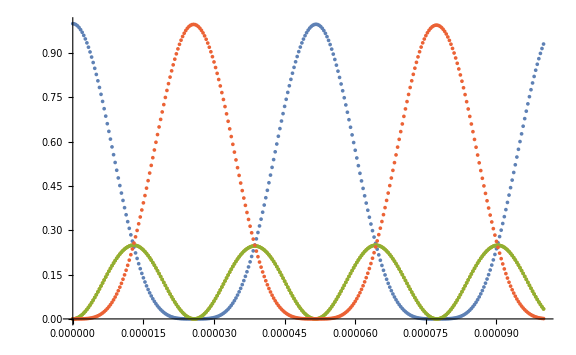

```mathematica
ListPlot[resPopsPoints4//Transpose,ImageSize->Large,DataRange->{tmin3,tmax3}]
```

This matches what we have for sample case 1.